```mathematica
params={Subscript[k, 1]->1,Subscript[k, 2]->2,Subscript[k, 3]->3,C1->10};
eqns={
R'[t]==Subscript[k, 1] g[t]-Subscript[k, 2] g[t]R[t]-Subscript[k, 2] M[t]R[t],
g'[t]==-Subscript[k, 2]g[t]R[t]+Subscript[k, 3](C1-g[t]),
M'[t]==-Subscript[k, 2]M[t]R[t]+Subscript[k, 3](C2-M[t])
};
inits={R[0]==0,g[0]==C1,M[0]==C2};
tf=1;
```

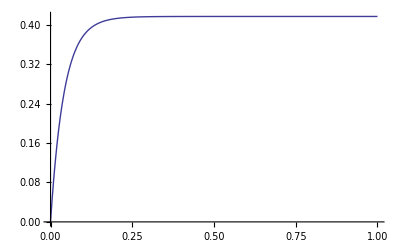

```mathematica
sol=NDSolve[eqns∪inits/.C2->2/.params,{R[t],g[t],M[t]},{t,0,tf}];
g1=Plot[R[t]/.sol,{t,0,tf},PlotRange->All]
```

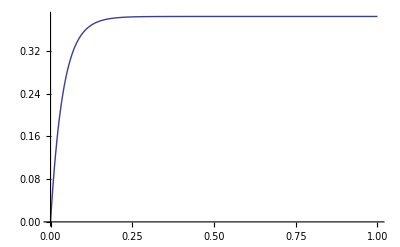

```mathematica
sol=NDSolve[eqns∪inits/.C2->3/.params,{R[t],g[t],M[t]},{t,0,tf}];
g2=Plot[R[t]/.sol,{t,0,tf},PlotRange->All]
```

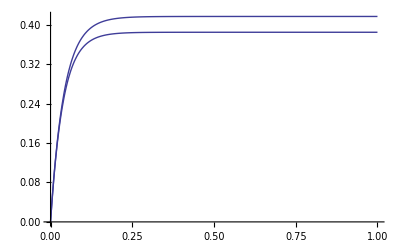

```mathematica
Show[g1,g2]
```

```mathematica
Solve[{
0==Subscript[k, 1] g[t]-Subscript[k, 2] g[t]R[t]-Subscript[k, 2] M[t]R[t],
0==-Subscript[k, 2]g[t]R[t]+Subscript[k, 3](C1-g[t]),
0==-Subscript[k, 2]M[t]R[t]+Subscript[k, 3](C2-M[t])
},{R[t],g[t],M[t]}]//Simplify
```

{{M[t]→(C2 (C1+C2) k_3)/(C1 k_1+(C1+C2) k_3),g[t]→(C1 (C1+C2) k_3)/(C1 k_1+(C1+C2) k_3),R[t]→(C1 k_1)/((C1+C2) k_2)}}

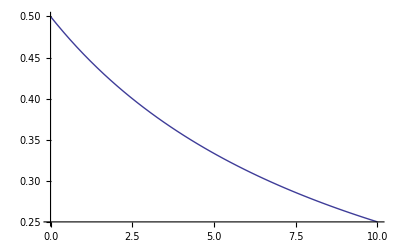

```mathematica
Plot[(C1 Subscript[k, 1])/((C1+C2) Subscript[k, 2])/.params,{C2,0,10}]
```

```mathematica
Needs["VectorFieldPlots`"]
```

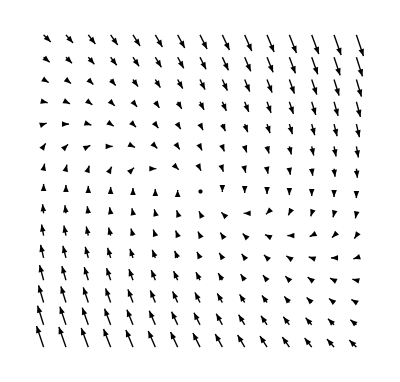

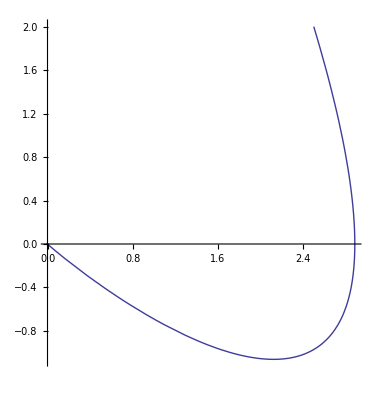

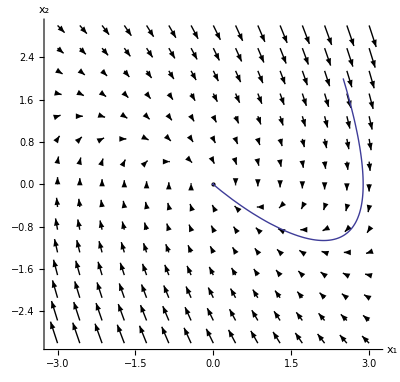

```mathematica
g1=VectorFieldPlot[{y,-x-2y}, {x, -3,3}, {y, -3, 3},Axes->True,AxesLabel->{"x_1","x_2"}]
sol=NDSolve[{x'[t]==y[t],y'[t]==-x[t]-2y[t],x[0]==2.5,y[0]==2},{x[t],y[t]},{t,0,50}];
g2=ParametricPlot[{x[t],y[t]}/.sol,{t,0,50},Axes->True,PlotRange->All]
Show[g1,g2,Axes->True,PlotRange->All,AxesLabel->{"x_1","x_2"}]
```

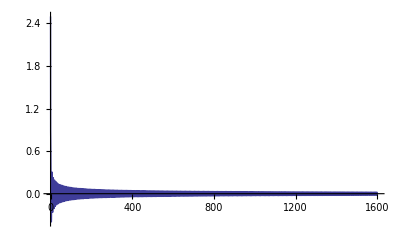

```mathematica
Plot[x[t]/.sol,{t,0,1600},PlotRange->All]
```

```mathematica
f={y-x(x^2+y^2),-x-y(x^2+y^2)};
A={
{D[f⟦1⟧,x],D[f⟦1⟧,y]},
{D[f⟦2⟧,x],D[f⟦2⟧,y]}
}/.x->0/.y->0
Eigenvalues[A]
```

{{0,1},{-1,0}}

{ⅈ,-ⅈ}

```mathematica
Simplify[D[1/2(x[t]^2+y[t]^2),t]/.{x'[t]-> y[t]-x[t](x[t]^2+y[t]^2),y'[t]-> -x[t]-y[t](x[t]^2+y[t]^2)}]
```

-(x[t]^2+y[t]^2)^2

```mathematica
D[f,x]
D[f,y]
```

{-3 x^2-y^2,-1-2 x y}

{1-2 x y,-x^2-3 y^2}

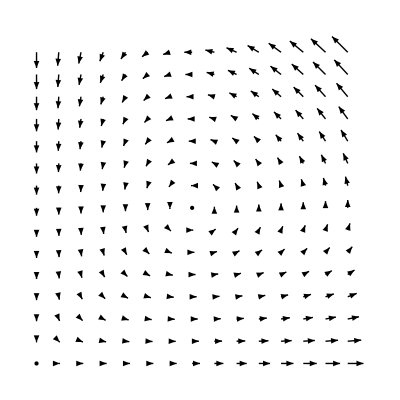

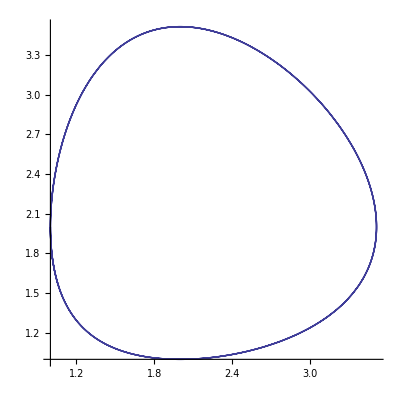

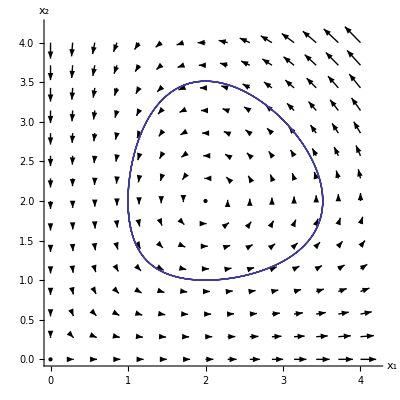

```mathematica
g1=VectorFieldPlot[{2x-x y,x y - 2y}, {x, 0,4}, {y, 0, 4},Axes->True,AxesLabel->{"x_1","x_2"}]
tf=10;
sol=NDSolve[{x'[t]==2x[t]-x[t]y[t],y'[t]==x[t]y[t]-2y[t],x[0]==1,y[0]==2},{x[t],y[t]},{t,0,tf}];
g2=ParametricPlot[{x[t],y[t]}/.sol,{t,0,tf},Axes->True,PlotRange->All]
Show[g1,g2,Axes->True,PlotRange->All,AxesLabel->{"x_1","x_2"}]
```

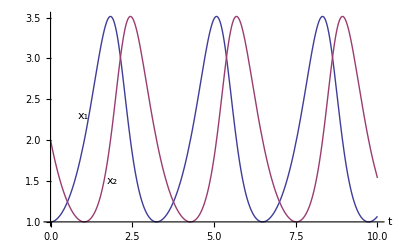

```mathematica
g3=Plot[{x[t]/.sol,y[t]/.sol},{t,0,10}];
Show[g3,Graphics[{Text["x_1",{1,2.3}],Text["x_2",{1.9,1.5}]}],AxesLabel->{"t",""}]
```

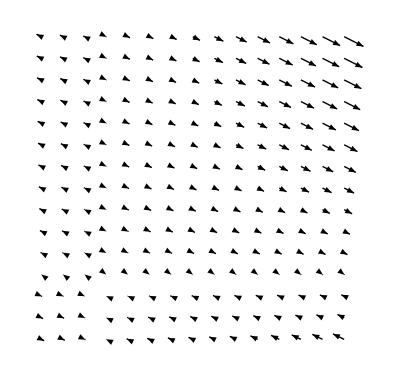

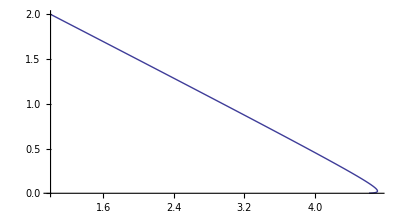

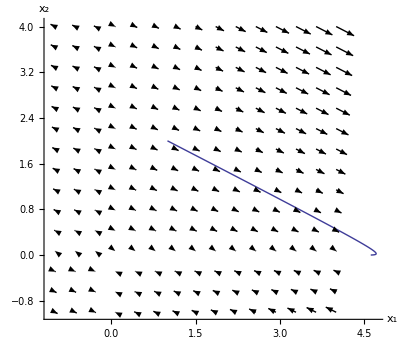

```mathematica
g1=VectorFieldPlot[{(2x y)/(5+y)-0.01x,-0.5(2x y)/(5+y)}, {x, -1,4}, {y, -1, 4},Axes->True,AxesLabel->{"x_1","x_2"}]
tf=10;
sol=NDSolve[{x'[t]==(2x[t] y[t])/(5+y[t])-0.01x[t],y'[t]==-0.5(2x[t] y[t])/(5+y[t]),x[0]==1,y[0]==2},{x[t],y[t]},{t,0,tf}];
g2=ParametricPlot[{x[t],y[t]}/.sol,{t,0,tf},Axes->True,PlotRange->All]
Show[g1,g2,Axes->True,PlotRange->All,AxesLabel->{"x_1","x_2"}]
```

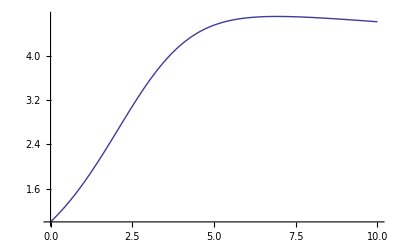

```mathematica
Plot[x[t]/.sol,{t,0,tf}]
```

```mathematica
f={-x-y+x y,-y-x y};
A={
{D[f⟦1⟧,x],D[f⟦1⟧,y]},
{D[f⟦2⟧,x],D[f⟦2⟧,y]}
};
A//MatrixForm
A/.{x->-1,y->1/2}//MatrixForm
Eigenvalues[A/.{x->0,y->0}]
Eigenvalues[A/.{x->-1,y->1/2}]
```

(-1+y | -1+x
-y | -1-x)

(-1/2 | -2
-1/2 | 0)

{-1,-1}

{1/4 (-1-√17),1/4 (-1+√17)}

```mathematica
Solve[{0==-x-y+x y,-y-x y==0},{x,y}]
```

{{x→0,y→0},{y→1/2,x→-1}}

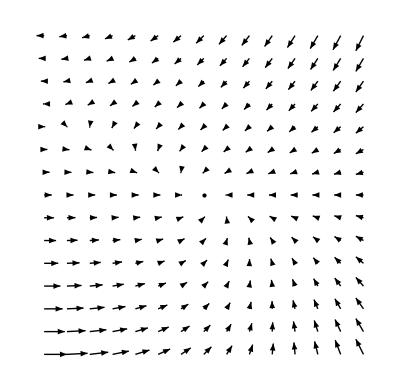

```mathematica
VectorFieldPlot[{-x-y+x y,-y-x y}, {x, -1,1}, {y, -1, 1},Axes->True,AxesLabel->{"x_1","x_2"}]
```